# Plot Elements

## Tradition Approach

```mathematica
SeedRandom[19870716];
```

```mathematica
data = (RandomVariate[BinormalDistribution[#,{0.3,0.3},0],10]&/@{{2,3},{1,1}})~Join~{Flatten[(RandomVariate[BinormalDistribution[#,{0.3,0.3},0],10]&/@{{4,1},{-1,3},{-1,-1}}),1]};
```

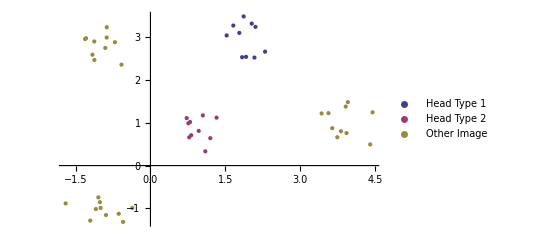

```mathematica
g1=ListPlot[data,PlotStyle->PointSize[Large],PlotLegends->Placed[PointLegend[{"Head Type 1","Head Type 2","Other Image"},LegendMarkerSize->10,LegendFunction->Frame],Above]]
```

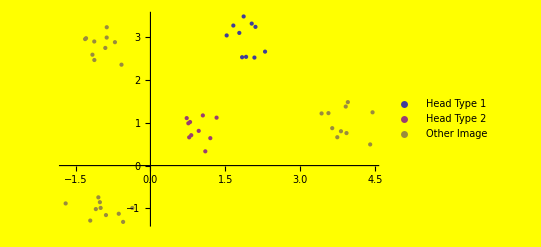

```mathematica
g1=ListPlot[data,PlotStyle->PointSize[Large],PlotLegends->Placed[PointLegend[{"Head Type 1","Head Type 2","Other Image"},LegendMarkerSize->10,LegendFunction->Frame],Above],Background->Yellow]
```

```mathematica
Export["D:/final_21.pdf",g1]
```

D:/final_21.pdf

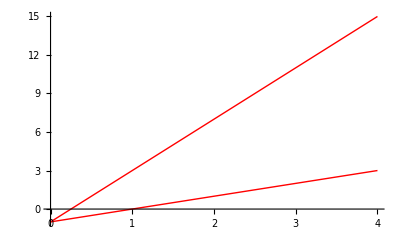

```mathematica
g2  = Plot[{4x-1,x-1},{x,0,4},PlotStyle->{Directive[Red,Thick],Directive[Red,Thick]}]
```

```mathematica
final12=Show[g1,g2]
```

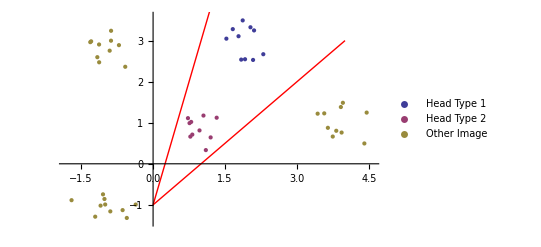

```mathematica
Export["D:/final_12.pdf",final12]
```

D:/final_12.pdf

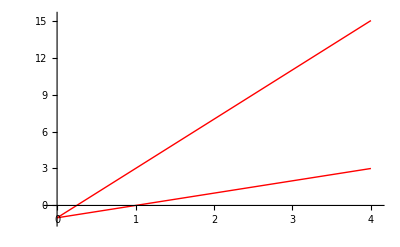

```mathematica
g3  = Plot[{4x-1,x-1},{x,0,4},PlotStyle->{Directive[Red,Thick],Directive[Red,Thick]}]
```

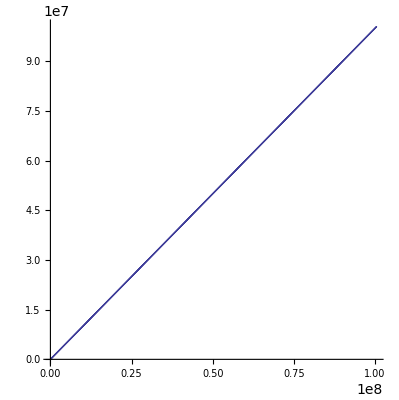

```mathematica
PolarPlot[5/(1+Cos[t-(5π)/4])-2,{t,-π/2,π/2}]
```

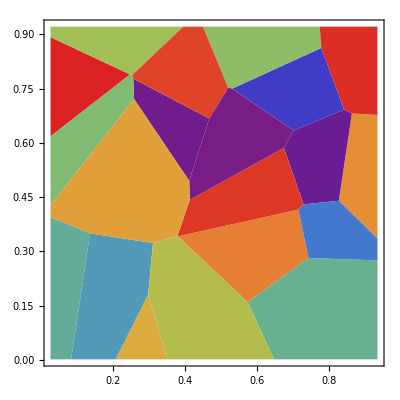

```mathematica
layer0=ListDensityPlot[RandomReal[{},{20,3}],InterpolationOrder->0,Mesh->None,ColorFunction->"Rainbow"]
```

```mathematica
Export["D:/layer0.png",layer0]
```

D:/layer0.png